```mathematica
(*Mathematica*)
```

```mathematica
(*Hyperelliptic:
Hyper-Weierstass*)
```

```mathematica
(* This set of equations is developed in the Weierstrass cubic elliptic pattern*)
```

```mathematica
w2[z_]=ExpandAll[6*Product[z-r[i],{i,5}]]
```

6 z^5-6 z^4 r[1]-6 z^4 r[2]+6 z^3 r[1] r[2]-6 z^4 r[3]+6 z^3 r[1] r[3]+6 z^3 r[2] r[3]-6 z^2 r[1] r[2] r[3]-6 z^4 r[4]+6 z^3 r[1] r[4]+6 z^3 r[2] r[4]-6 z^2 r[1] r[2] r[4]+6 z^3 r[3] r[4]-6 z^2 r[1] r[3] r[4]-6 z^2 r[2] r[3] r[4]+6 z r[1] r[2] r[3] r[4]-6 z^4 r[5]+6 z^3 r[1] r[5]+6 z^3 r[2] r[5]-6 z^2 r[1] r[2] r[5]+6 z^3 r[3] r[5]-6 z^2 r[1] r[3] r[5]-6 z^2 r[2] r[3] r[5]+6 z r[1] r[2] r[3] r[5]+6 z^3 r[4] r[5]-6 z^2 r[1] r[4] r[5]-6 z^2 r[2] r[4] r[5]+6 z r[1] r[2] r[4] r[5]-6 z^2 r[3] r[4] r[5]+6 z r[1] r[3] r[4] r[5]+6 z r[2] r[3] r[4] r[5]-6 r[1] r[2] r[3] r[4] r[5]

```mathematica
v=CoefficientList[w2[z],z]
```

{-6 r[1] r[2] r[3] r[4] r[5],6 r[1] r[2] r[3] r[4]+6 r[1] r[2] r[3] r[5]+6 r[1] r[2] r[4] r[5]+6 r[1] r[3] r[4] r[5]+6 r[2] r[3] r[4] r[5],-6 r[1] r[2] r[3]-6 r[1] r[2] r[4]-6 r[1] r[3] r[4]-6 r[2] r[3] r[4]-6 r[1] r[2] r[5]-6 r[1] r[3] r[5]-6 r[2] r[3] r[5]-6 r[1] r[4] r[5]-6 r[2] r[4] r[5]-6 r[3] r[4] r[5],6 r[1] r[2]+6 r[1] r[3]+6 r[2] r[3]+6 r[1] r[4]+6 r[2] r[4]+6 r[3] r[4]+6 r[1] r[5]+6 r[2] r[5]+6 r[3] r[5]+6 r[4] r[5],-6 r[1]-6 r[2]-6 r[3]-6 r[4]-6 r[5],6}

```mathematica
(*independent coefficients*)
```

```mathematica
g5=v[[1]];
g4=v[[2]];
```

```mathematica
(*dependent coefficients*)
```

```mathematica
(*The dependent conditions are pretty specific: they appear to map a specific conformal manifold.*)
```

```mathematica
g3=v[[3]];
g2=v[[4]];
g1=v[[5]];
```

```mathematica
(*root dependences Reduced*)
```

```mathematica
Reduce[{g1 == 0, g2 == 0, g3 == 0}, {r[1], r[2], r[3], r[4], r[5]}]
```

(r[3]==Root[r[1]^3+r[1]^2 r[2]+r[1] r[2]^2+r[2]^3+(r[1]^2+r[1] r[2]+r[2]^2) #1+(r[1]+r[2]) #1^2+#1^3&,1]||r[3]==Root[r[1]^3+r[1]^2 r[2]+r[1] r[2]^2+r[2]^3+(r[1]^2+r[1] r[2]+r[2]^2) #1+(r[1]+r[2]) #1^2+#1^3&,2]||r[3]==Root[r[1]^3+r[1]^2 r[2]+r[1] r[2]^2+r[2]^3+(r[1]^2+r[1] r[2]+r[2]^2) #1+(r[1]+r[2]) #1^2+#1^3&,3])&&(r[4]==1/2 (-r[1]-r[2]-r[3]-√(-3 r[1]^2-2 r[1] r[2]-3 r[2]^2-2 r[1] r[3]-2 r[2] r[3]-3 r[3]^2))||r[4]==1/2 (-r[1]-r[2]-r[3]+√(-3 r[1]^2-2 r[1] r[2]-3 r[2]^2-2 r[1] r[3]-2 r[2] r[3]-3 r[3]^2)))&&r[5]==-r[1]-r[2]-r[3]-r[4]

```mathematica
(*six solutions exist in pairs*)
```

```mathematica
w6=w2[z]/.NSolve[{g1 == 0, g2 == 0, g3 == 0}, {r[1], r[2], r[3], r[4], r[5]}]//Chop
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(121297 r[1])/150069-(136940 r[2])/150069+(61196 r[3])/50023-(54409 r[4])/50023+(104356 r[5])/150069 == 1.

NSolve::infsolns: Infinite solution set has dimension at least 2. Returning intersection of solutions with (61057 r[1])/68868-(48047 r[2])/45912-(54589 r[3])/68868+(14156 r[4])/17217+(58453 r[5])/45912 == 1.

{(-0.232409-0.414074 ⅈ)+(0.853923-0.144833 ⅈ) z+6 z^5,(-0.232409+0.414074 ⅈ)+(0.853923+0.144833 ⅈ) z+6 z^5,(0.0337631+0.0291751 ⅈ)-(0.346305+0.12025 ⅈ) z+6 z^5,(0.0337631-0.0291751 ⅈ)-(0.346305-0.12025 ⅈ) z+6 z^5,(-0.803648-0.70565 ⅈ)+(1.751-0.400838 ⅈ) z+6 z^5,(-0.803648+0.70565 ⅈ)+(1.751+0.400838 ⅈ) z+6 z^5}

```mathematica
u=Table[CoefficientList[w6[[i]],z],{i,6}]
```

{{-0.232409-0.414074 ⅈ,0.853923-0.144833 ⅈ,0,0,0,6},{-0.232409+0.414074 ⅈ,0.853923+0.144833 ⅈ,0,0,0,6},{0.0337631+0.0291751 ⅈ,-0.346305-0.12025 ⅈ,0,0,0,6},{0.0337631-0.0291751 ⅈ,-0.346305+0.12025 ⅈ,0,0,0,6},{-0.803648-0.70565 ⅈ,1.751-0.400838 ⅈ,0,0,0,6},{-0.803648+0.70565 ⅈ,1.751+0.400838 ⅈ,0,0,0,6}}

```mathematica
j=FullSimplify[ExpandAll[g4^5/(g4^5-6^5*g5^4)]]
```

(r[2] r[3] r[4] r[5]+r[1] (r[3] r[4] r[5]+r[2] (r[3] r[4]+(r[3]+r[4]) r[5])))^5/(r[2]^5 r[3]^5 r[4]^5 r[5]^5+5 r[1] r[2]^4 r[3]^4 r[4]^4 r[5]^4 (r[3] r[4] r[5]+r[2] (r[3] r[4]+(r[3]+r[4]) r[5]))+10 r[1]^2 r[2]^3 r[3]^3 r[4]^3 r[5]^3 (r[3] r[4] r[5]+r[2] (r[3] r[4]+(r[3]+r[4]) r[5]))^2+10 r[1]^3 r[2]^2 r[3]^2 r[4]^2 r[5]^2 (r[3] r[4] r[5]+r[2] (r[3] r[4]+(r[3]+r[4]) r[5]))^3+r[1]^5 (r[3] r[4] r[5]+r[2] (r[3] r[4]+(r[3]+r[4]) r[5]))^5+r[1]^4 r[2] r[3] r[4] r[5] (5 r[3]^4 r[4]^4 r[5]^4+20 r[2] r[3]^3 r[4]^3 r[5]^3 (r[3] r[4]+(r[3]+r[4]) r[5])+30 r[2]^2 r[3]^2 r[4]^2 r[5]^2 (r[3] r[4]+(r[3]+r[4]) r[5])^2+5 r[2]^4 (r[3] r[4]+(r[3]+r[4]) r[5])^4+4 r[2]^3 r[3] r[4] r[5] (5 r[3]^3 r[4]^3+15 r[3]^2 r[4]^2 (r[3]+r[4]) r[5]+3 r[3] r[4] (5 r[3]^2-98 r[3] r[4]+5 r[4]^2) r[5]^2+5 (r[3]+r[4])^3 r[5]^3)))

```mathematica
j5=Table[u[[i,2]]^5/(u[[i,2]]^5-6^5*u[[i,1]]^4),{i,6}]
```

{-0.000438988-0.00115274 ⅈ,-0.000438988+0.00115274 ⅈ,0.105816-0.164072 ⅈ,0.105816+0.164072 ⅈ,0.00119179-0.00139687 ⅈ,0.00119179+0.00139687 ⅈ}

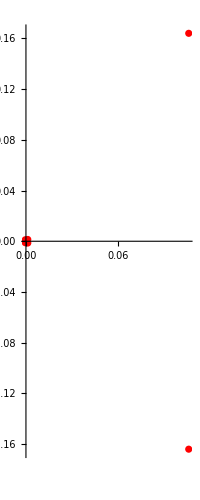

```mathematica
ComplexListPlot[j5,ImageSize->Full,PlotStyle->Red,PlotRange->All]
```

```mathematica
Norm/@j5
```

{0.0012335,0.0012335,0.195235,0.195235,0.0018362,0.0018362}

```mathematica
p[z_]=ExpandAll[Apply[Times,w6]]//Chop
```

0.000513498-0.00948059 z+0.0640997 z^2-0.182986 z^3+0.380051 z^4-0.326578 z^5-0.866542 z^6+2.73533 z^7-5.34112 z^8+4.16006 z^9+3.7652 z^10+0.115529 z^11-25.8227 z^12+70.0104 z^13-67.5921 z^14-163.138 z^15+513.033 z^16-540.52 z^17+419.266 z^18+2564.05 z^20-6663.89 z^21+8402.88 z^22-15587.7 z^25+35126. z^26+46656 z^30

```mathematica
roots=z/.NSolve[p[z]==0,z]
```

{-0.618098-0.575136 ⅈ,-0.618098+0.575136 ⅈ,-0.608488-0.486069 ⅈ,-0.608488+0.486069 ⅈ,-0.520627-0.0505319 ⅈ,-0.520627+0.0505319 ⅈ,-0.516763-0.369437 ⅈ,-0.516763+0.369437 ⅈ,-0.49736-0.502891 ⅈ,-0.49736+0.502891 ⅈ,-0.0717475-0.488567 ⅈ,-0.0717475+0.488567 ⅈ,0.0164698-0.509371 ⅈ,0.0164698+0.509371 ⅈ,0.0914541-0.436697 ⅈ,0.0914541+0.436697 ⅈ,0.113109-0.0454107 ⅈ,0.113109+0.0454107 ⅈ,0.199679-0.49887 ⅈ,0.199679+0.49887 ⅈ,0.410976-0.556245 ⅈ,0.410976+0.556245 ⅈ,0.458098-0.666252 ⅈ,0.458098+0.666252 ⅈ,0.462796-0.0259253 ⅈ,0.462796+0.0259253 ⅈ,0.511693-0.253002 ⅈ,0.511693+0.253002 ⅈ,0.56881-0.25645 ⅈ,0.56881+0.25645 ⅈ}

```mathematica
(*Weeks-Meyerhoff root volume form*)
```

```mathematica
vv=Table[N[Im[PolyLog[2,roots[[i]]]+Log[Abs[roots[[i]]]] Log[1-roots[[i]]]]],{i,Length[roots]}]
```

{-0.498856,0.498856,-0.448859,0.448859,-0.0622013,0.0622013,-0.404098,0.404098,-0.514981,0.514981,-0.763308,0.763308,-0.821774,0.821774,-0.808949,0.808949,-0.155847,0.155847,-0.882611,0.882611,-0.946925,0.946925,-0.991249,0.991249,-0.0718793,0.0718793,-0.614374,0.614374,-0.621588,0.621588}

```mathematica
Max[vv]
```

0.991249

```mathematica
Min[Abs[vv]]
```

0.0622013

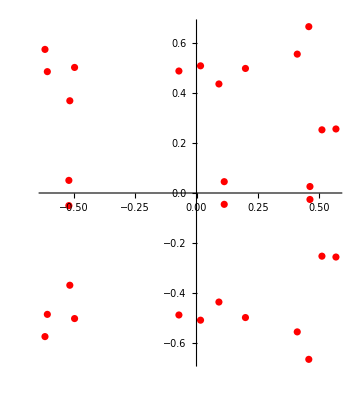

```mathematica
ComplexListPlot[roots,ImageSize->Full,PlotStyle->Red,PlotRange->All]
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Transpose[CompanionMatrix[p[z],z] ]
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{-1.10061×10^-8,2.03202×10^-7,-1.37388×10^-6,3.92203×10^-6,-8.14581×10^-6,6.9997×10^-6,0.000018573,-0.0000586277,0.000114479,-0.0000891644,-0.0000807013,-2.47618×10^-6,0.00055347,-0.00150057,0.00144873,0.00349662,-0.0109961,0.0115852,-0.00898633,0,-0.0549565,0.14283,-0.180103,0,0,0.334098,-0.752873,0,0,0}}

```mathematica
ei=Eigenvalues[m]
```

{-0.618098+0.575136 ⅈ,-0.618098-0.575136 ⅈ,0.458098+0.666252 ⅈ,0.458098-0.666252 ⅈ,-0.608488+0.486069 ⅈ,-0.608488-0.486069 ⅈ,-0.49736+0.502891 ⅈ,-0.49736-0.502891 ⅈ,0.410976+0.556245 ⅈ,0.410976-0.556245 ⅈ,-0.516763+0.369437 ⅈ,-0.516763-0.369437 ⅈ,0.56881+0.25645 ⅈ,0.56881-0.25645 ⅈ,0.511693+0.253002 ⅈ,0.511693-0.253002 ⅈ,0.199679+0.49887 ⅈ,0.199679-0.49887 ⅈ,-0.520627+0.0505319 ⅈ,-0.520627-0.0505319 ⅈ,0.0164698+0.509371 ⅈ,0.0164698-0.509371 ⅈ,-0.0717475+0.488567 ⅈ,-0.0717475-0.488567 ⅈ,0.462796+0.0259253 ⅈ,0.462796-0.0259253 ⅈ,0.0914541+0.436697 ⅈ,0.0914541-0.436697 ⅈ,0.113109+0.0454107 ⅈ,0.113109-0.0454107 ⅈ}

```mathematica
Norm/@ei
```

{0.844291,0.844291,0.808545,0.808545,0.778794,0.778794,0.707295,0.707295,0.6916,0.6916,0.635238,0.635238,0.623948,0.623948,0.570824,0.570824,0.537348,0.537348,0.523074,0.523074,0.509638,0.509638,0.493807,0.493807,0.463521,0.463521,0.44617,0.44617,0.121884,0.121884}

```mathematica
max=Max[Norm/@ei]
```

0.844291

```mathematica
min=Min[Norm/@ei]
```

0.121884

```mathematica
max-min
```

0.722407

```mathematica
(*Weighted Graph:16 border:14 internal*)
```

```mathematica
gf=WeightedAdjacencyGraph[m,ImageSize->Full,VertexLabels->"Name"]
AbsoluteOptions[gf,VertexCoordinates]
{VertexList[gf],EdgeList[gf]}
```

{VertexCoordinates→{{1.28622,0.729769},{0.297935,0.47181},{1.00851,0.851089},{0.,0.979136},{1.18867,0.416997},{0.899395,0.281034},{1.09376,1.28827},{1.17815,1.60269},{1.49039,0.305938},{0.720269,0.564754},{1.68158,0.82753},{0.955504,0.},{0.578925,0.890648},{0.306791,0.171639},{0.595426,1.29794},{1.58134,0.565539},{1.6097,1.18926},{0.0253491,0.529077},{1.23892,0.0977514},{0.30729,1.04847},{1.40266,1.01388},{0.619661,1.63433},{0.362628,1.48731},{0.578363,0.308372},{1.39458,1.3975},{0.140617,1.29051},{0.208086,0.771452},{0.890624,1.59009},{0.844349,1.10877},{0.599355,0.0229472}}}

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{1->1,1->2,1->3,1->4,1->5,1->6,1->7,1->8,1->9,1->10,1->11,1->12,1->13,1->14,1->15,1->16,1->17,1->18,1->19,1->20,1->21,1->22,1->23,1->24,1->25,1->26,1->27,1->28,1->29,1->30,2->1,2->2,2->3,2->4,2->5,2->6,2->7,2->8,2->9,2->10,2->11,2->12,2->13,2->14,2->15,2->16,2->17,2->18,2->19,2->20,2->21,2->22,2->23,2->24,2->25,2->26,2->27,2->28,2->29,2->30,3->1,3->2,3->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->12,3->13,3->14,3->15,3->16,3->17,3->18,3->19,3->20,3->21,3->22,3->23,3->24,3->25,3->26,3->27,3->28,3->29,3->30,4->1,4->2,4->3,4->4,4->5,4->6,4->7,4->8,4->9,4->10,4->11,4->12,4->13,4->14,4->15,4->16,4->17,4->18,4->19,4->20,4->21,4->22,4->23,4->24,4->25,4->26,4->27,4->28,4->29,4->30,5->1,5->2,5->3,5->4,5->5,5->6,5->7,5->8,5->9,5->10,5->11,5->12,5->13,5->14,5->15,5->16,5->17,5->18,5->19,5->20,5->21,5->22,5->23,5->24,5->25,5->26,5->27,5->28,5->29,5->30,6->1,6->2,6->3,6->4,6->5,6->6,6->7,6->8,6->9,6->10,6->11,6->12,6->13,6->14,6->15,6->16,6->17,6->18,6->19,6->20,6->21,6->22,6->23,6->24,6->25,6->26,6->27,6->28,6->29,6->30,7->1,7->2,7->3,7->4,7->5,7->6,7->7,7->8,7->9,7->10,7->11,7->12,7->13,7->14,7->15,7->16,7->17,7->18,7->19,7->20,7->21,7->22,7->23,7->24,7->25,7->26,7->27,7->28,7->29,7->30,8->1,8->2,8->3,8->4,8->5,8->6,8->7,8->8,8->9,8->10,8->11,8->12,8->13,8->14,8->15,8->16,8->17,8->18,8->19,8->20,8->21,8->22,8->23,8->24,8->25,8->26,8->27,8->28,8->29,8->30,9->1,9->2,9->3,9->4,9->5,9->6,9->7,9->8,9->9,9->10,9->11,9->12,9->13,9->14,9->15,9->16,9->17,9->18,9->19,9->20,9->21,9->22,9->23,9->24,9->25,9->26,9->27,9->28,9->29,9->30,10->1,10->2,10->3,10->4,10->5,10->6,10->7,10->8,10->9,10->10,10->11,10->12,10->13,10->14,10->15,10->16,10->17,10->18,10->19,10->20,10->21,10->22,10->23,10->24,10->25,10->26,10->27,10->28,10->29,10->30,11->1,11->2,11->3,11->4,11->5,11->6,11->7,11->8,11->9,11->10,11->11,11->12,11->13,11->14,11->15,11->16,11->17,11->18,11->19,11->20,11->21,11->22,11->23,11->24,11->25,11->26,11->27,11->28,11->29,11->30,12->1,12->2,12->3,12->4,12->5,12->6,12->7,12->8,12->9,12->10,12->11,12->12,12->13,12->14,12->15,12->16,12->17,12->18,12->19,12->20,12->21,12->22,12->23,12->24,12->25,12->26,12->27,12->28,12->29,12->30,13->1,13->2,13->3,13->4,13->5,13->6,13->7,13->8,13->9,13->10,13->11,13->12,13->13,13->14,13->15,13->16,13->17,13->18,13->19,13->20,13->21,13->22,13->23,13->24,13->25,13->26,13->27,13->28,13->29,13->30,14->1,14->2,14->3,14->4,14->5,14->6,14->7,14->8,14->9,14->10,14->11,14->12,14->13,14->14,14->15,14->16,14->17,14->18,14->19,14->20,14->21,14->22,14->23,14->24,14->25,14->26,14->27,14->28,14->29,14->30,15->1,15->2,15->3,15->4,15->5,15->6,15->7,15->8,15->9,15->10,15->11,15->12,15->13,15->14,15->15,15->16,15->17,15->18,15->19,15->20,15->21,15->22,15->23,15->24,15->25,15->26,15->27,15->28,15->29,15->30,16->1,16->2,16->3,16->4,16->5,16->6,16->7,16->8,16->9,16->10,16->11,16->12,16->13,16->14,16->15,16->16,16->17,16->18,16->19,16->20,16->21,16->22,16->23,16->24,16->25,16->26,16->27,16->28,16->29,16->30,17->1,17->2,17->3,17->4,17->5,17->6,17->7,17->8,17->9,17->10,17->11,17->12,17->13,17->14,17->15,17->16,17->17,17->18,17->19,17->20,17->21,17->22,17->23,17->24,17->25,17->26,17->27,17->28,17->29,17->30,18->1,18->2,18->3,18->4,18->5,18->6,18->7,18->8,18->9,18->10,18->11,18->12,18->13,18->14,18->15,18->16,18->17,18->18,18->19,18->20,18->21,18->22,18->23,18->24,18->25,18->26,18->27,18->28,18->29,18->30,19->1,19->2,19->3,19->4,19->5,19->6,19->7,19->8,19->9,19->10,19->11,19->12,19->13,19->14,19->15,19->16,19->17,19->18,19->19,19->20,19->21,19->22,19->23,19->24,19->25,19->26,19->27,19->28,19->29,19->30,20->1,20->2,20->3,20->4,20->5,20->6,20->7,20->8,20->9,20->10,20->11,20->12,20->13,20->14,20->15,20->16,20->17,20->18,20->19,20->20,20->21,20->22,20->23,20->24,20->25,20->26,20->27,20->28,20->29,20->30,21->1,21->2,21->3,21->4,21->5,21->6,21->7,21->8,21->9,21->10,21->11,21->12,21->13,21->14,21->15,21->16,21->17,21->18,21->19,21->20,21->21,21->22,21->23,21->24,21->25,21->26,21->27,21->28,21->29,21->30,22->1,22->2,22->3,22->4,22->5,22->6,22->7,22->8,22->9,22->10,22->11,22->12,22->13,22->14,22->15,22->16,22->17,22->18,22->19,22->20,22->21,22->22,22->23,22->24,22->25,22->26,22->27,22->28,22->29,22->30,23->1,23->2,23->3,23->4,23->5,23->6,23->7,23->8,23->9,23->10,23->11,23->12,23->13,23->14,23->15,23->16,23->17,23->18,23->19,23->20,23->21,23->22,23->23,23->24,23->25,23->26,23->27,23->28,23->29,23->30,24->1,24->2,24->3,24->4,24->5,24->6,24->7,24->8,24->9,24->10,24->11,24->12,24->13,24->14,24->15,24->16,24->17,24->18,24->19,24->20,24->21,24->22,24->23,24->24,24->25,24->26,24->27,24->28,24->29,24->30,25->1,25->2,25->3,25->4,25->5,25->6,25->7,25->8,25->9,25->10,25->11,25->12,25->13,25->14,25->15,25->16,25->17,25->18,25->19,25->20,25->21,25->22,25->23,25->24,25->25,25->26,25->27,25->28,25->29,25->30,26->1,26->2,26->3,26->4,26->5,26->6,26->7,26->8,26->9,26->10,26->11,26->12,26->13,26->14,26->15,26->16,26->17,26->18,26->19,26->20,26->21,26->22,26->23,26->24,26->25,26->26,26->27,26->28,26->29,26->30,27->1,27->2,27->3,27->4,27->5,27->6,27->7,27->8,27->9,27->10,27->11,27->12,27->13,27->14,27->15,27->16,27->17,27->18,27->19,27->20,27->21,27->22,27->23,27->24,27->25,27->26,27->27,27->28,27->29,27->30,28->1,28->2,28->3,28->4,28->5,28->6,28->7,28->8,28->9,28->10,28->11,28->12,28->13,28->14,28->15,28->16,28->17,28->18,28->19,28->20,28->21,28->22,28->23,28->24,28->25,28->26,28->27,28->28,28->29,28->30,29->1,29->2,29->3,29->4,29->5,29->6,29->7,29->8,29->9,29->10,29->11,29->12,29->13,29->14,29->15,29->16,29->17,29->18,29->19,29->20,29->21,29->22,29->23,29->24,29->25,29->26,29->27,29->28,29->29,29->30,30->1,30->2,30->3,30->4,30->5,30->6,30->7,30->8,30->9,30->10,30->11,30->12,30->13,30->14,30->15,30->16,30->17,30->18,30->19,30->20,30->21,30->22,30->23,30->24,30->25,30->26,30->27,30->28,30->29,30->30}}

```mathematica
(*How can this very specific solution be interpreted as an hyperbolic manifold solution?*)
(*A 30 edge group in a Siefert-Webber an hyperbolic Dodecahedral manifold as an hyper-Fuchsian triangle group:
{2,3,7,-30}*)
```

```mathematica
(*visualizations as 3d convex hull root polyhedron and Voronoi diagram*)
```

```mathematica
(* Mathematica*)
<<ComputationalGeometry`
```

```mathematica
(*Reference:Marc Bellon,Elements of dodecahedral cosmology.*)
```

```mathematica
Clear[r,phi,pa,pts]
```

```mathematica
pa[z_]=0.0005134984241342432-0.009480593211169916 z+0.06409970693342719 z^2-0.18298609741283045 z^3+0.38005071910618765 z^4-0.3265780801410887 z^5-0.8665421359330104 z^6+2.735334251095321 z^7-5.341118075815059 z^8+4.160055563029244 z^9+3.765200875108038 z^10+0.11552877018886232 z^11-25.8226929277473 z^12+70.01040554312932 z^13-67.59207680783867 z^14-163.13842222148412 z^15+513.0331712348917 z^16-540.5195214661553 z^17+419.2661146716151 z^18+2564.0500156067274 z^20-6663.888023933286 z^21+8402.881514187104 z^22-15587.678581959255 z^25+35126.029497481766 z^26+46656 z^30
```

0.000513498-0.00948059 z+0.0640997 z^2-0.182986 z^3+0.380051 z^4-0.326578 z^5-0.866542 z^6+2.73533 z^7-5.34112 z^8+4.16006 z^9+3.7652 z^10+0.115529 z^11-25.8227 z^12+70.0104 z^13-67.5921 z^14-163.138 z^15+513.033 z^16-540.52 z^17+419.266 z^18+2564.05 z^20-6663.89 z^21+8402.88 z^22-15587.7 z^25+35126. z^26+46656 z^30

```mathematica
a0={Re[x],Im[x]}/.NSolve[pa[x]==0,x];
```

```mathematica
Length[a0]
```

30

```mathematica
pts=Union[{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)/.NSolve[pa[x]==0,x]]//Chop
```

{{-0.817564,-0.0793525,0.570344},{-0.817564,0.0793525,0.570344},{-0.757523,-0.60512,0.244927},{-0.757523,0.60512,0.244927},{-0.736377,-0.526441,0.424981},{-0.736377,0.526441,0.424981},{-0.721729,-0.671563,0.16766},{-0.721729,0.671563,0.16766},{-0.663029,-0.670402,0.333097},{-0.663029,0.670402,0.333097},{-0.115364,-0.785575,0.607916},{-0.115364,0.785575,0.607916},{0.0261482,-0.808699,0.587641},{0.0261482,0.808699,0.587641},{0.152542,-0.728393,0.667963},{0.152542,0.728393,0.667963},{0.222907,-0.0894919,0.970723},{0.222907,0.0894919,0.970723},{0.309882,-0.774196,0.5519},{0.309882,0.774196,0.5519},{0.554013,-0.805749,0.209376},{0.554013,0.805749,0.209376},{0.556008,-0.752542,0.352896},{0.556008,0.752542,0.352896},{0.761896,-0.0426806,0.646291},{0.761896,0.0426806,0.646291},{0.771877,-0.381648,0.508478},{0.771877,0.381648,0.508478},{0.818837,-0.369176,0.439563},{0.818837,0.369176,0.439563}}

```mathematica
maxx=Max[Table[pts[[i,1]],{i,30}]]
maxy=Max[Table[pts[[i,2]],{i,30}]]
maxz=Max[Table[pts[[i,3]],{i,30}]]
```

0.818837

0.808699

0.970723

```mathematica
(*Geometric average estimate of Polyhedron manifold volume*)
```

```mathematica
(maxx*maxy*maxz)^(1/3)
```

0.863031

```mathematica
ptsn=Table[Hue[Norm[x/.NSolve[pa[x]==0,x][[i]]]/1.75],{i,Length[pts]}]
```

{Hue[0.482451868914635],Hue[0.482451868914635],Hue[0.4450251558915317],Hue[0.4450251558915317],Hue[0.2988991630307347],Hue[0.2988991630307347],Hue[0.3629933299176164],Hue[0.3629933299176164],Hue[0.4041684193155071],Hue[0.4041684193155071],Hue[0.2821756228297571],Hue[0.2821756228297571],Hue[0.29122144346841566],Hue[0.29122144346841566],Hue[0.25495430643350364],Hue[0.25495430643350364],Hue[0.06964814964039934],Hue[0.06964814964039934],Hue[0.3070557969472107],Hue[0.3070557969472107],Hue[0.39519979639632985],Hue[0.39519979639632985],Hue[0.46202579826919593],Hue[0.46202579826919593],Hue[0.26486927621854583],Hue[0.26486927621854583],Hue[0.3261850482202282],Hue[0.3261850482202282],Hue[0.35654155251032776],Hue[0.35654155251032776]}

```mathematica
(* Voronoi diagram*)
```

```mathematica
a=Union[Most/@pts];
```

```mathematica
g1=Show[{
DiagramPlot[a],
Graphics[{Red,PointSize[.005],Point[a]}]
},PlotRange->All,Frame->True,ImageSize->Full]
```

```mathematica
g2=Show[Graphics3D[{Red,PointSize[0.0375/3],Point/@pts}],Axes->True,ImageSize->1000,ViewPoint->{5,5,5}]
```

```mathematica
(*(* Voronoi diagram*)
g1=Show[{
DiagramPlot[a0,LabelPoints->False]/._Point:>{},
Graphics[{Red,PointSize[.005],Point[a0]}]
},PlotRange->All,Frame->True,PlotRangeClipping->True,ImageSize->1000]
(* 3d projection of polyhedron*)*)
```

```mathematica
(* convex hull: MathWorld Library*)
<<ConvexHull`
```

```mathematica
hull0=ConvexHull3D[pts];
```

```mathematica
Length[hull0]
```

49

```mathematica
hull1=Flatten[Table[If[i≤Length[ptsn],{ptsn[[i]],hull0[[i]]},{}],{i,Length[hull0]}]];
```

```mathematica
hull3=Show[{g2,Graphics3D[{hull0,hull={Opacity[0.5],hull1}},ImageSize->Full,Boxed->False,Background->Black,ViewPoint->Right]},ImageSize->Full,Boxed->False,Background->Black,ViewPoint->{2,2,2}]
```

```mathematica
(*end*)
```